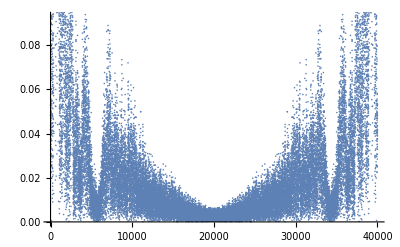

0

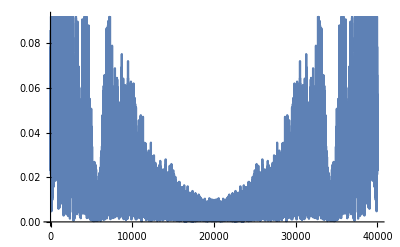

```mathematica
d261=Import["/Users/lykos/QEA/BSet2Files/Disturbance261.wav"];
x261=d261//AudioData;
Fourier[x261]//Abs//ListPlot
x261[[Ordering[Fourier@x261,-2]]]=0

InverseFourier[x261]//Abs//ListLinePlot
```

```mathematica
Cos[Subscript[ω, t]*t]
```

Cos[t ω_t]

```mathematica
part=TrigToExp[Cos[t Subscript[ω, t]]]
```

1/2 ⅇ^(-ⅈ t ω_t)+1/2 ⅇ^(ⅈ t ω_t)

```mathematica
Cos[Subscript[ω, c]*t]
```

Cos[t ω_c]

```mathematica
TrigToExp[Cos[t Subscript[ω, c]]^2]
```

1/2+1/4 ⅇ^(-2 ⅈ t ω_c)+1/4 ⅇ^(2 ⅈ t ω_c)

```mathematica
bass=Import["/Users/lykos/QEA/InClass3Files/bass1.wav"];
x=AudioData[bass];
bass
```

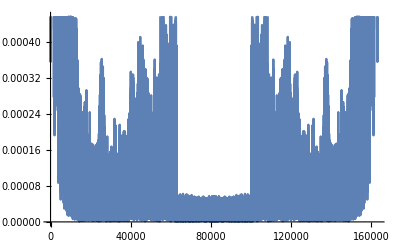

```mathematica
Fourier[x]//Abs//ListLinePlot
```

```mathematica
fft[stuff_]:=Fourier[stuff,FourierParameters->{1,-1}];

fft[x]//Abs//ListLinePlot
```

{-92.1585+1.16851×10^-14 ⅈ,-6.93291+4.43249 ⅈ,1.3941-1.6341 ⅈ,1.64764-5.852 ⅈ,163164,1.64764+5.852 ⅈ,1.3941+1.6341 ⅈ,-6.93291-4.43249 ⅈ}
 |  |  |  |